#### Gauge Independent Scalars from time-like Geodesics for Kerr Spacetime [spin parameter a = J/M = 0.1 term]

```mathematica
Clear[coord, metric, inversemetric, affine, t, r, θ,ϕ];
```

```mathematica
kvar={t,r,θ,ϕ};
n=Length[kvar];
Kmet =  {  {g00[r,θ],0,0,g03[r,θ] },
            {0,g11[r,θ],0,0},
            {0,0,g22[r,θ],0},
            {g03[r,θ],0,0,g33[r,θ]}    };
```

```mathematica
Kmet
```

{{g00[r,θ],0,0,g03[r,θ]},{0,g11[r,θ],0,0},{0,0,g22[r,θ],0},{g03[r,θ],0,0,g33[r,θ]}}

```mathematica
Kcompa ={
g00->(-( 1 - 2 M #1/Σ[#1,#2]) &),
g03 -> ( -(2 M a #1 Sin[#2]^2/Σ[#1,#2] )&),
g11 ->( Σ[#1,#2]/Δ[#1 ] &),
g22 ->( Σ[#1,#2] &),
g33 ->  ( A[#1,#2] Sin[#2]^2/ Σ[#1,#2]&) };
```

```mathematica
Kcompa
```

{g00→(-(1-(2 M #1)/Σ[#1,#2])&),g03→(-(2 M a #1 Sin[#2]^2)/Σ[#1,#2]&),g11→(Σ[#1,#2]/Δ[#1]&),g22→(Σ[#1,#2]&),g33→((A[#1,#2] Sin[#2]^2)/Σ[#1,#2]&)}

```mathematica
Kcompb={Σ-> ( ( #1^2+ a^2 Cos[#2]^2)&),
    Δ->(	(#1^2-2 M #1 +a^2)&),
		A->(( (#1^2+a^2)^2-a^2 Δ[#1] Sin[#2]^2)&) 
 };
```

```mathematica
metric=Kmet/.Kcompa //.Kcompb;
```

```mathematica
metric //MatrixForm;
```

```mathematica
metric
```

{{-1+(2 M r)/(r^2+a^2 Cos[θ]^2),0,0,-(2 a M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)},{0,(r^2+a^2 Cos[θ]^2)/(a^2-2 M r+r^2),0,0},{0,0,r^2+a^2 Cos[θ]^2,0},{-(2 a M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2),0,0,(Sin[θ]^2 ((a^2+r^2)^2-a^2 (a^2-2 M r+r^2) Sin[θ]^2))/(r^2+a^2 Cos[θ]^2)}}

```mathematica
inversemetric= Simplify[Inverse[metric]];
```

```mathematica
affine:=affine=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],kvar[[k]]]+D[metric[[s,k]],kvar[[j]]]-
D[metric[[j,k]],kvar[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]]
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}],{i,1,n},{j,1,n},{k,1,j}]
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2, 2}];
```

```mathematica
riemann:=riemann=Simplify[Table[
D[affine[[i,j,l]],kvar[[k]] ]-D[affine[[i,j,k]],kvar[[l]] ]+
Sum[affine[[s,j,l]] affine[[i,k,s]]-affine[[s,j,k]] affine[[i,l,s]],
{s,1,n}],
{i,1,n},{j,1,n},{k,1,n},{l,1,n}] ];
```

```mathematica
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}],{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2, 2}];
```

```mathematica
lriemann=Simplify[Table[Sum[riemann[[l,j,k,m]]metric[[l,i]],{l,1,n}],{i,1,n},{j,1,n},{k,1,n},{m,1,n}]];
```

```mathematica
ricci:=ricci=Simplify[Table[Sum[riemann[[l,j,l,m]],{l,1,n}],{j,1,n},{m,1,n}]];
```

```mathematica
listricci:=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}],{j,1,n},{l,1,n}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2, 2}]
```

{}

```mathematica
scalar=FullSimplify[Sum[inversemetric[[i,j]]ricci[[i,j]],{i,1,n},{j,1,n}]]
```

0

```mathematica
affine=affine/.{t->t[s], r->r[s], θ->θ[s], ϕ->ϕ[s]};
```

```mathematica
riemann=riemann/.{t->t[s], r->r[s], θ->θ[s], ϕ->ϕ[s]};
```

```mathematica
lriemann=lriemann/.{t->t[s], r->r[s], θ->θ[s], ϕ->ϕ[s]};
```

```mathematica
usgab=metric/.{t->t[s], r->r[s], θ->θ[s], ϕ->ϕ[s]};
```

```mathematica
U={ut[s], ur[s], uθ[s], uϕ[s]};
Y={yt[s], yr[s], yθ[s], yϕ[s]};
X={xt[s], xr[s],xθ[s], xϕ[s]};
Z={zt[s], zr[s],zθ[s], zϕ[s]};
RHS[a_]:= -Sum[affine[[a,i,j]] U[[i]] U[[j]],{i,1,4},{j,1,4}];
RHSV[a_]:= -Sum[affine[[a,i,j]] U[[i]] Y[[j]],{i,1,4},{j,1,4}];
RHSVV[a_]:= -Sum[affine[[a,i,j]] U[[i]] X[[j]],{i,1,4},{j,1,4}];
RHSVVV[a_]:= -Sum[affine[[a,i,j]] U[[i]] Z[[j]],{i,1,4},{j,1,4}];
```

```mathematica
eqns={ut'[s] == RHS[1], ur'[s] == RHS[2], uθ'[s] == RHS[3], uϕ'[s] == RHS[4],yt'[s] == RHSV[1], yr'[s]==RHSV[2], yθ'[s] ==  RHSV[3], yϕ'[s]==RHSV[4],xt'[s] == RHSVV[1], xr'[s]==RHSVV[2], xθ'[s] ==  RHSVV[3], xϕ'[s]==RHSVV[4],zt'[s] == RHSVVV[1],zr'[s]==RHSVVV[2], zθ'[s] ==  RHSVVV[3], zϕ'[s]==RHSVVV[4],t'[s] == ut[s], r'[s] == ur[s], θ'[s] == uθ[s], ϕ'[s]==uϕ[s]};
```

```mathematica
R0=10; θ0=Pi/2; ϕ0=0; rdot0 = 0; a = 0.1;θdot=0; ϕdot=Sqrt[M]/(R0*Sqrt[R0-3M]);
U0=U/.s->0;
```

```mathematica
icond={t[0] ==0, r[0] == R0, θ[0] == θ0, ϕ[0]==ϕ0, ur[0]==rdot0, uθ[0]==θdot, uϕ[0]==ϕdot, ut[0] == ut0, yt[0]==0, yr[0]==Sqrt[1-2 M/R0], yθ[0]==0, yϕ[0]==0,xϕ[0]==0, xt[0]==0, xr[0]==0, xθ[0]==1/R0, zθ[0]==0,zr[0]==0,zt[0]==(ϕdot*R0)/Sqrt[(-1+2M/R0)*(ϕdot^2*R0^2)+(1-2M/R0)^2*ut0^2],zϕ[0]==(1-2M/R0)*ut0/(R0*Sqrt[(-1+2M/R0)*(ϕdot^2*R0^2)+(1-2M/R0)^2*ut0^2])} ;
```

```mathematica
M=1;
ut0=ut[0]/.Solve[((U0.metric.U0)/.{r->R0, θ->θ0, ϕ->ϕ0, ur[0]->rdot0, uθ[0]->θdot, uϕ[0]->ϕdot})==-1, ut[0]][[2]];
```

```mathematica
Solve[((U0.metric.U0)/.{r->R0, θ->θ0, ϕ->ϕ0, ur[0]->rdot0, uθ[0]->θdot, uϕ[0]->ϕdot})==-1, ut[0]][[2]]
```

{ut[0]→1.19429}

```mathematica
icond;
alleq=Join[eqns, icond];
alleq;
uθ[s];
```

```mathematica
sol=NDSolve[alleq, {t[s], r[s], θ[s], ϕ[s], ut[s], ur[s], uθ[s],uϕ[s], yt[s], yr[s], yθ[s], yϕ[s], xt[s], xr[s], xθ[s], xϕ[s],zt[s],zr[s],zθ[s],zϕ[s]}, {s,0,1000}, AccuracyGoal->10,WorkingPrecision->10,  MaxSteps->Infinity][[1]];
```

NDSolve::precw: The precision of the differential equation ({{ut'[s]==(4 (0.01+0.01 Cos[«1»]-2 Power[«2»]) (0.01+r[«1»]^2) ur[s] ut[s])/((0.01+Times[«2»]) (0.01+Times[«2»]+Times[«2»])^2)+(0.08 r[s] Sin[2 θ[«1»]] ut[s] uθ[s])/(0.01+«1»+Times[«2»])^2-(0.4 («5»+«1») Sin[«1»]^2 ur[s] uϕ[s])/((0.01+Times[«2»]) («1»)^2)-(0.016 Cos[θ[s]] r[s] Sin[θ[«1»]]^3 uθ[s] uϕ[s])/(0.01+Times[«2»]+Times[«2»])^2,«9»,«30»},{},{},{},{}}) is less than WorkingPrecision (10.).

```mathematica
Clear[normalization];
normalization=(U.usgab.U)/.sol;
normalization/.s->1
```

-1.

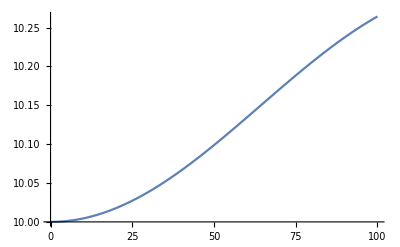

```mathematica
(uθ[s]/.sol)/.s->1;
Plot[Evaluate[r[s]/.sol], {s,0,100},PlotRange->All]
```

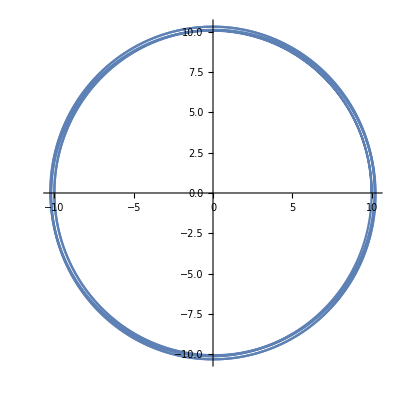

```mathematica
ParametricPlot[{r[s]Cos[ϕ[s]],r[s]Sin[ϕ[s]]}/.sol,{s,0,1000},PlotPoints->10000]
```

```mathematica
Scalaruxux[s_] = Simplify[Sum[lriemann[[i,j,k,l]] U[[i]]Y[[j]]U[[k]]Y[[l]],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]]/.sol;
```

```mathematica
tabuxux=Table[{i/2, Scalaruxux [i/2]},{i,0,400}];
```

```mathematica
tabuxux >> "/tmp/scalaroutN1uxux"
```

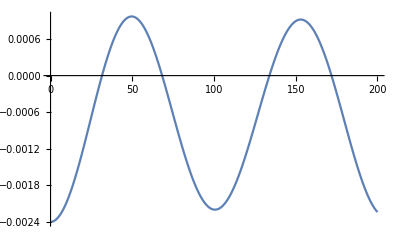

```mathematica
ListLinePlot[tabuxux]
```

```mathematica
Scalaruxxy[s_] = Simplify[Sum[lriemann[[i,j,k,l]] U[[i]]X[[j]]X[[k]]Y[[l]],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]]/.sol;
```

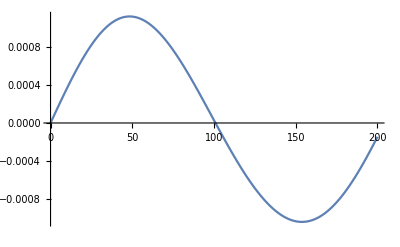

```mathematica
tabuxxy=Table[{i/2, Scalaruxxy [i/2]},{i,0,400}];
tabuxxy >> "/tmp/scalaroutN1uxxy"
ListLinePlot[tabuxxy]
```

```mathematica
Scalaruxxz[s_] = Simplify[Sum[lriemann[[i,j,k,l]] U[[i]]X[[j]]X[[k]]Z[[l]],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]]/.sol;
```

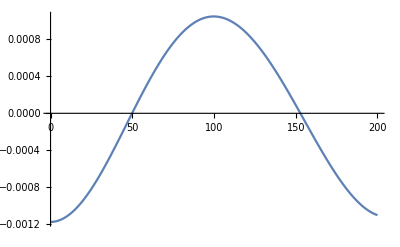

```mathematica
tabuxxz=Table[{i/2, Scalaruxxz[i/2]},{i,0,400}];
tabuxxz >> "/tmp/scalaroutN1uxxz"
ListLinePlot[tabuxxz]
```